# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.909047955948669×10^9

#### 変数

```mathematica
date="20230830"
```

20230830

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20230830.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20230830.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

14988323 207813984 7760524276 log-20230830.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=ci.P~5

```mathematica
SetDirectory[dir["ci"]]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=ci.P~5

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
dir["ci"]<>"/"<>file["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=ci.P~5/self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

2520923

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{2520923}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90234×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

DateList::str: String  cannot be interpreted as a date in format Automatic.

AbsoluteTime::arg: Argument DateList[] cannot be interpreted as a date or time input.

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-08-29T15:00:00Z
log.ci0001.aws.wa02.yobi
66.249.71.35
host":"-
user":"-
3.90234×10^9
method":"GET
https://cir.nii.ac.jp/crid/1390846609780418816
code":"200
size":"13748
-
agent":"Googlebot/2.1 (+http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.71.35\"
request_time":"0.046
upstream_response_time":"0.044"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "ajax-loader.gif".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-08-29T15:00:00Z
log.ci0001.aws.wa02.yobi
3.112.79.151
host":"-
user":"-
3.90234×10^9
method":"GET
https://cir.nii.ac.jp/
code":"200
size":"9977
-
agent":"Mozilla/5.0 (X11; Linux x86_64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/97.0.4692.71 Safari/537.36
http_x_forwarded_for":"\"3.112.79.151\"
request_time":"0.070
upstream_response_time":"0.072"}
toCRID[https://cir.nii.ac.jp/]
toCRID[-]

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=cs.R=.P=

```mathematica
SetDirectory[dir["cs"]]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=cs.R=.P=

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

29699

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{29699,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{29699,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/user/satoshi-yazawa@nii.ac.jp/nz87j-osfstorage-znnjp057/nbtags/cell/2667dc12-cfd6-11ea-9dc1-0242ac160003-16-ec91-0297-ddcf-a9a8-a76d-d9ef-40ec-bf60-19d7-9fde

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-08-30T00:00:00.867851043+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-08-29T15:00:39Z
log.cs0002.ksw.wa01.yobi
122.214.152.139
stream":"stdout
user":"-
3.90234×10^9
date_time":"29/Aug/2023:15:00:38 +0000
https://jupyter.cs.rcos.nii.ac.jp/user/satoshi-yazawa@nii.ac.jp/nz87j-osfstorage-znnjp057/nbtags/cell/989e1750-bbf0-11ea-aaab-0242ac110002-19-f399-423b-30ea-565c-c450-effe-9571-08e4-6547-ea3c
method":"GET
code":"304
https://jupyter.cs.rcos.nii.ac.jp/user/satoshi-yazawa@nii.ac.jp/nz87j-osfstorage-znnjp057/notebooks/2023-08-29_01_OperationHub%E3%82%92AWS%E3%81%AB%E6%A7%8B%E7%AF%89.ipynb
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.0.0 Safari/537.36
size":"0
hostname":"fluentd-bllnp"}

### データ(la)

8/30 以前のデータに対応。

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=la.T~ea.A~hc.A~go.A~bot.P~api

```mathematica
SetDirectory[dir["la"]]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=la.T~ea.A~hc.A~go.A~bot.P~api

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

373536

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{373536}

```mathematica
(strSplt1["la"]=Select[strSplt1["la","pre"],Length[#]==12&])//Dimensions
```

{3,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
rp["la"]//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
(strSplt1R["la"]=Map[#[[rp["la"]]]&,strSplt1["la"]])//Dimensions
```

{3,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["la"][[1]][[8]]
```

path":"/wp-login.php

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["la"][[1]][[6]]
```

date_time":"29/Aug/2023:18:50:46 +0000

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]
```

29/Aug/2023:18:50:46

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList
```

{2023,8,29,18,50,46.}

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.90232×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2023-08-29T18:50:46Z
log.la0003.aws.wa01.yobi
http_x_forwarded_for":"64.90.40.100
size":"-
method":"GET
3.90236×10^9
code":"302
https://lms.nii.ac.jp/wp-login.php
{"user":"-
session_id":"-"}
http://analytics.la.lms.nii.ac.jp/wp-login.php
agent":"Mozilla/5.0 (X11; Fedora; Linux x86_64; rv:94.0) Gecko/20100101 Firefox/95.0

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCC["la"][[1]][[3]]
```

http_x_forwarded_for":"64.90.40.100

```mathematica
strSplt1CCC["la"][[1]][[3]]//ip["la"]
```

64.90.40.100

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{3,12}

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=wk.P~4.A~bot

```mathematica
SetDirectory[dir["wk"]]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=wk.P~4.A~bot

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

572

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{572,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{572,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-08-29T15:15:00+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.90234×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-08-29T20:19:36Z
log.wk1001.oci.wa01.yobi
23.191.80.18
user":"-
method":"GET
3.90236×10^9
code":"404
https://jdcat.jsps.go.jp/records/42739/export/json/.env
size":"1935
http_x_forwarded_for":"23.191.80.18"}
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10.15; rv:77.0) Gecko/20100101 Firefox/77.0

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
(*Timing[(strSplt1CCCC[3]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]*)
```

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{29.2904,{2551197}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{2551197}

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{2551197}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

171

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

171

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{2551197}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

11

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

11

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

179

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

179

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{28.3754,{2520923}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-08-29T21:37:28Z.08log.ci0001.aws.wa04.yobi
{"remote":"66.249.79.6
-
user":"-
time":"2023-08-30T06:37:28+0900
AbsoluteTime[DateList[]]
path":"/crid/1390006275936280320
https://cir.nii.ac.jp/00
size":"14719
referer":"-
zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.79.6\"
request_time":"0.014
upstream_response_time":"0.013"}
toCRID[https://cir.nii.ac.jp/00]
toCRID[zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)]
1

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{2520923}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690857923898207616,1690576448924459648,1690013498971780864,1690013498970963584,1690294973948512512,1690013498969706368,1690013498976445184,1690013498976445184,1690013498976445184,1690013498976445184,1690013498976445184,1690013498969706368,1690013498976532608,1690013498967385472,1690013498974547968,1690013498978919296,1690013498964842496,1690294973957106304,1690294973946873088,1690013498965767424,1690013498965767424,1690013498976268160,1690576448924226688,1690576448922196736,1690013498976407424,1690857923896514944,1690857923901082112,1690857977695145728,1690576448923518464,1690857923906274176,1690857923906274176,1690576448923813248,1690576448930898816,1690013498976459904,1690857923909274368,1690576448930230144,1690576448934388736,1690576448927939584,1690576448924233728,1690576448924233728,1690013498969026688,1690013498977616512,1690857923901553664,1690576448930598656,1690857977695145728,1690294973945783168,1690576448933584512,1690857923901881472,1690857923911210624,1690576448929666432,1690294973957704192,1690576448925001856,1690576448930691200,1690294973953792256,1690013498980499712,1690013498979016832,1690857923896972160,1690013498965717632,1690576448922196736,1690576448922196736,1690857977695145728,1690857977695145728,1690857977695145728,1690294973942661120,1690294973952643840,1690576448920165120,1690013498967091840,1690294973953250688,1690294973956788480,1690576448924109312,1690294973953331072,1690013498970190592,1690013498970190592,1690857923910322048,1690857923905796736,1690857923901251072,1690857977695145728,1690857977695145728,1690013498966372608,1690294973945589120,1690013498977616512,1690294973947133184,1690857977695145728,1690857923906980992,1690013498976523776,1690013498976259200,1690013498975115008,1690857923901785088,1690576448923394048,1690857923906283904,1690576448930598656,1690857923901553664,1690576448930598656,1690857923901489152,1690576448924459648,1690294973945589120,1690294973946873088,1690013498969026688,1690294973945589120,1690857923906274176,1690294973945783168,1690294973952655616,1690294973953331072,1690576448927939584,1690013498967040000,1690857923900580736,1690294973953553152,1690576448920303872,1690857977695145728,1690857977695145728,1690576448922037248,1690576448922988928,1690013498977023232,1690857977695145728,1690857923896622976,1690857923911356544,1690576448934541952,1690576448932674304,1690857923900535424,1690857923899082240,1690576448921933056,1690576448921560064,1690294973945052288,1690576448921560064,1690576448934541952,1690857923896633856,1690294973958337280,1690294973953136000,1690857923899082240,1690857923910372864,1690013498967751936,1690857923895685120,1690576448933286400,1690294973953136000,1690857923906243712,1690294973954766720,1690857923898811520,1690857923907938432,1690294973957574528,1690294973957600768,1690294973942815360,1690576448928126464,1690294973942815360,1690294973953239040,1690294973944754432,1690576448934314624,1690294973953239040,1690294973942137216,1690576448932674304,1690294973957947264,1690576448922196736,1690576448919603584,1690857923896635520,1690857923906024320,1690576448927218048,1690857923900438144,1690857923907938432,1690294973957600768,1690294973946087552,1690013498966444544,1690576448922196736,1690576448927218048,1690013498967942272,1690576448921667456,1690294973958337280,1690294973951980672,1690294973955067136,1690576448933286400,1690576448928126464,1690857923900438144,1690294973948792704}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690576448924459648,1690013498976445184,1690013498976445184,1690576448924226688,1690857923906274176,1690857923906274176,1690576448930598656,1690576448930598656,1690576448933584512,1690013498966372608,1690013498966372608}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964842496,1690013498965717632,1690013498965767424,1690013498966372608,1690013498966444544,1690013498967040000,1690013498967091840,1690013498967385472,1690013498967751936,1690013498967942272,1690013498969026688,1690013498969706368,1690013498970190592,1690013498970963584,1690013498971780864,1690013498974547968,1690013498975115008,1690013498976259200,1690013498976268160,1690013498976407424,1690013498976445184,1690013498976459904,1690013498976523776,1690013498976532608,1690013498977023232,1690013498977616512,1690013498978919296,1690013498979016832,1690013498980499712,1690294973942137216,1690294973942661120,1690294973942815360,1690294973944754432,1690294973945052288,1690294973945589120,1690294973945783168,1690294973946087552,1690294973946873088,1690294973947133184,1690294973948512512,1690294973948792704,1690294973951980672,1690294973952643840,1690294973952655616,1690294973953136000,1690294973953239040,1690294973953250688,1690294973953331072,1690294973953553152,1690294973953792256,1690294973954766720,1690294973955067136,1690294973956788480,1690294973957106304,1690294973957574528,1690294973957600768,1690294973957704192,1690294973957947264,1690294973958337280,1690576448919603584,1690576448920165120,1690576448920303872,1690576448921560064,1690576448921667456,1690576448921933056,1690576448922037248,1690576448922196736,1690576448922988928,1690576448923394048,1690576448923518464,1690576448923813248,1690576448924109312,1690576448924226688,1690576448924233728,1690576448924459648,1690576448925001856,1690576448927218048,1690576448927939584,1690576448928126464,1690576448929666432,1690576448930230144,1690576448930598656,1690576448930691200,1690576448930898816,1690576448932674304,1690576448933286400,1690576448933584512,1690576448934314624,1690576448934388736,1690576448934541952,1690857923895685120,1690857923896514944,1690857923896622976,1690857923896633856,1690857923896635520,1690857923896972160,1690857923898207616,1690857923898811520,1690857923899082240,1690857923900438144,1690857923900535424,1690857923900580736,1690857923901082112,1690857923901251072,1690857923901489152,1690857923901553664,1690857923901785088,1690857923901881472,1690857923905796736,1690857923906024320,1690857923906243712,1690857923906274176,1690857923906283904,1690857923906980992,1690857923907938432,1690857923909274368,1690857923910322048,1690857923910372864,1690857923911210624,1690857923911356544,1690857977695145728}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964842496→True,1690013498965717632→True,1690013498965767424→True,1690013498966372608→True,1690013498966444544→True,1690013498967040000→True,1690013498967091840→True,1690013498967385472→True,1690013498967751936→True,1690013498967942272→True,1690013498969026688→True,1690013498969706368→True,1690013498970190592→True,1690013498970963584→True,1690013498971780864→True,1690013498974547968→True,1690013498975115008→True,1690013498976259200→True,1690013498976268160→True,1690013498976407424→True,1690013498976445184→True,1690013498976459904→True,1690013498976523776→True,1690013498976532608→True,1690013498977023232→True,1690013498977616512→True,1690013498978919296→True,1690013498979016832→True,1690013498980499712→True,1690294973942137216→True,1690294973942661120→True,1690294973942815360→True,1690294973944754432→True,1690294973945052288→True,1690294973945589120→True,1690294973945783168→True,1690294973946087552→True,1690294973946873088→True,1690294973947133184→True,1690294973948512512→True,1690294973948792704→True,1690294973951980672→True,1690294973952643840→True,1690294973952655616→True,1690294973953136000→True,1690294973953239040→True,1690294973953250688→True,1690294973953331072→True,1690294973953553152→True,1690294973953792256→True,1690294973954766720→True,1690294973955067136→True,1690294973956788480→True,1690294973957106304→True,1690294973957574528→True,1690294973957600768→True,1690294973957704192→True,1690294973957947264→True,1690294973958337280→True,1690576448919603584→True,1690576448920165120→True,1690576448920303872→True,1690576448921560064→True,1690576448921667456→True,1690576448921933056→True,1690576448922037248→True,1690576448922196736→True,1690576448922988928→True,1690576448923394048→True,1690576448923518464→True,1690576448923813248→True,1690576448924109312→True,1690576448924226688→True,1690576448924233728→True,1690576448924459648→True,1690576448925001856→True,1690576448927218048→True,1690576448927939584→True,1690576448928126464→True,1690576448929666432→True,1690576448930230144→True,1690576448930598656→True,1690576448930691200→True,1690576448930898816→True,1690576448932674304→True,1690576448933286400→True,1690576448933584512→True,1690576448934314624→True,1690576448934388736→True,1690576448934541952→True,1690857923895685120→True,1690857923896514944→True,1690857923896622976→True,1690857923896633856→True,1690857923896635520→True,1690857923896972160→True,1690857923898207616→True,1690857923898811520→True,1690857923899082240→True,1690857923900438144→True,1690857923900535424→True,1690857923900580736→True,1690857923901082112→True,1690857923901251072→True,1690857923901489152→True,1690857923901553664→True,1690857923901785088→True,1690857923901881472→True,1690857923905796736→True,1690857923906024320→True,1690857923906243712→True,1690857923906274176→True,1690857923906283904→True,1690857923906980992→True,1690857923907938432→True,1690857923909274368→True,1690857923910322048→True,1690857923910372864→True,1690857923911210624→True,1690857923911356544→True,1690857977695145728→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

132273

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{4.74273,{132273,1}}

```mathematica
idxLogS[4][[1]]
```

{{2023-08-29T21:37:28Z.08log.ci0001.aws.wa04.yobi,{"remote":"66.249.79.6,-,user":"-,time":"2023-08-30T06:37:28+0900,AbsoluteTime[DateList[]],path":"/crid/1390006275936280320,https://cir.nii.ac.jp/00,size":"14719,referer":"-,zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html),http_x_forwarded_for":"\"66.249.79.6\",request_time":"0.014,upstream_response_time":"0.013"},toCRID[https://cir.nii.ac.jp/00],toCRID[zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)],1}}

```mathematica
idxLogSinf[4][[1]]
```

{{{2023-08-29T21:37:28Z.08log.ci0001.aws.wa04.yobi,{"remote":"66.249.79.6,-,user":"-,time":"2023-08-30T06:37:28+0900,AbsoluteTime[DateList[]],path":"/crid/1390006275936280320,https://cir.nii.ac.jp/00,size":"14719,referer":"-,zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html),http_x_forwarded_for":"\"66.249.79.6\",request_time":"0.014,upstream_response_time":"0.013"},toCRID[https://cir.nii.ac.jp/00],toCRID[zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)],1}}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

/Volumes/elecom/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.009308,Null}

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

132273

上記がユーザー数。

ここでindexを作成。{date,{userID, story-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}]; (**)
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions] (**)
```

{197.86,{132273,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ](**)
```

{216.429,{132273,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{132273,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

{zilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.5845.110 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)https://cir.nii.ac.jp/00{AbsoluteTime[DateList[]],1}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{243386,3}

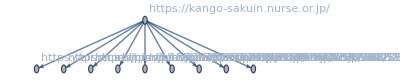
{20230830,{162,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{243386,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

{243386,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{225201,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{216734,3}

上が分離されたストーリー

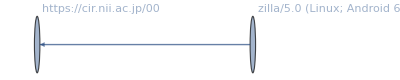
{20230830,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3[4][[1]]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
Directory[]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
(*Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",ckanName]]
Timing[Save["storyGrIdxFlDs3.save",ckanCridAC]]
Timing[Save["storyGrIdxFlDs3.save",ckanCridPLogPosAC]]
Timing[Save["storyGrIdxFlDs3.save",ckanCridRLogPosAC]]
Timing[Save["storyGrIdxFlDs3.save",ckanCridPRLogPosAC]]*)
```

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{216734}

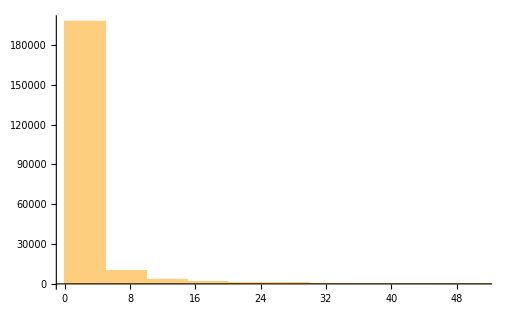

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{216734}

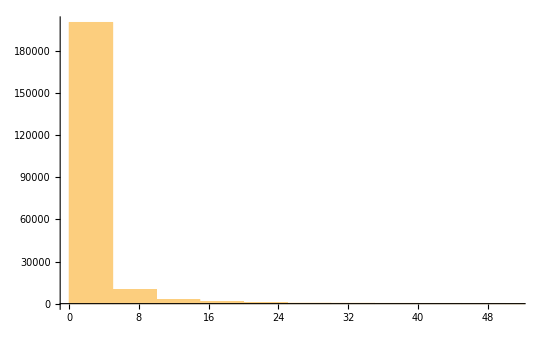

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{216734}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{216734}

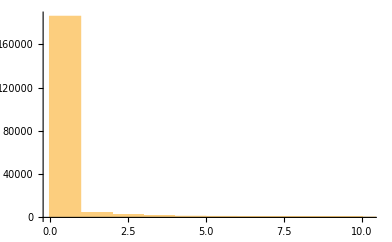

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{216734}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{216734}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{216734}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{216734}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{554fcae493e564ee0dc75bdf2ebf94caads|a:2:{s:3:\\x22num\\x22;s:72:\\x220,1 procedure analyse(extractvalue(rand(),concat(0x7e,version())),1)-- -\\x22;s:2:\\x22id\\x22;i:1;}}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{39,53,54,56,68,71,80,84,135,136,164,177,188,217,218,219,220,221,222,223,280,288,301,302,320,331,345,347,371,385,392,509,537,597,610,616,627,702,732,734,735,941,1276,1362,1493}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:analytics.la.lms.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:dashboard.la.lms.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:preview-binder.cs.rcos.nii.ac.jp,http:preview-jupyter.cs.rcos.nii.ac.jp,https:analytics.la.lms.nii.ac.jp:443,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii*ac.jp,https:cir.nii.ac.jp,https:cir.nii.ac.jp:443,https:cir-nii-ac-jp.ezproxy.tulips.tsukuba.ac.jp,https:feedback.cir.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:hannan-u.repo.nii.ac.jp,https:hokusho.repo.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:library.unii.ac.jp,https:lms.nii.ac.jp,https:nayoro.repo.nii.ac.jp,https:niu.repo.nii.ac.jp,https:nrid.nii.ac.jp,https:omnh.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp,https:support.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp,jdcat.jsps.go.jplogin}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{216734}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,119538},{1,97194},{3,2}}

```mathematica
(GrBasesTly[4]=Tally[ GrBases[4]])//Dimensions
```

{1502,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,203762},{2,12972}}

```mathematica
(GrNiiBasesTly[4]= Tally[GrNiiBases[4]])//Dimensions
```

{46,2}

```mathematica
TableForm[GrNiiBasesTly[4]]
```

https:cir.nii.ac.jp | 203655
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 11082
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 27
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 103
https:cir.nii.ac.jp
https:www.nii.ac.jp | 6
https:jdcat.jsps.go.jp | 32
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp | 75
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 7
https:cir.nii.ac.jp
https:support.nii.ac.jp | 76
https:cir.nii.ac.jp
https:omnh.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 1223
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 331
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 12
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 26
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 6
https:ci-nii-ac-jp.cdn.ampproject.org
https:cir.nii.ac.jp | 2
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 2
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:nayoro.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 2
https:cir.nii.ac.jp
https:cir-nii-ac-jp.ezproxy.tulips.tsukuba.ac.jp | 1
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 2
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 6
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 10
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:hannan-u.repo.nii.ac.jp | 1
http:dashboard.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 9
https:jdcat.jsps.go.jp
jdcat.jsps.go.jplogin | 1
https:cir.nii.ac.jp
https:niu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 7
https:cir.nii*ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:www.unii.ac.jp | 2
https:cir.nii.ac.jp
https:hokusho.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:library.unii.ac.jp | 1
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
http:preview-jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:redmine.devops.rcos.nii.ac.jp | 1
https:analytics.la.lms.nii.ac.jp:443
https:lms.nii.ac.jp | 1
http:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir.nii.ac.jp:443 | 1
http:preview-binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{216734}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{216734}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{216734}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{66,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{6,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{66,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{66,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{4,66,8,2,2,8,7,16,38,17,30,22,23,9,16,8,2,30,9,15,2,7,2,2,2,13,14,14,14,24,31,2,2,7,8,4,12,8,8,2,2,2,16,19,220,197,220,2,3,9,51,2,2,51,22,9,5,24,15,2,4,5,4,15,2,12}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{4625.,3060.,29277.,0.,0.,196.,26.,15753.,9516.,1273.,21556.,11944.,19399.,21660.,9823.,539.,0.,5463.,442.,45757.,0.,1427.,0.,0.,0.,2388.,2533.,2524.,1087.,578.,523.,0.,0.,112.,2791.,55.,12213.,3422.,2854.,0.,0.,246.,20890.,420.,16955.,3237.,3237.,0.,10057.,150.,1774.,0.,0.,23106.,1947.,363.,27.,4646.,26402.,146.,24766.,9381.,7.,726.,0.,664.}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->10,VertexCoordinates->coornew]
]
```

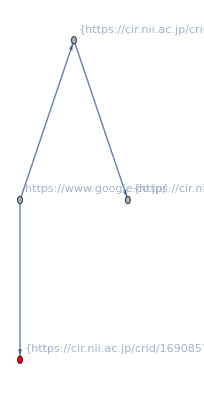
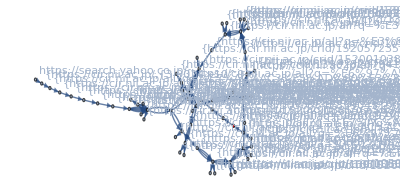
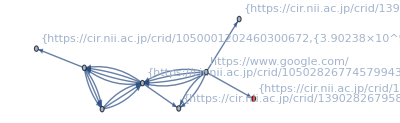
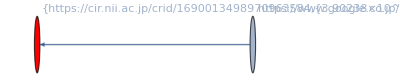
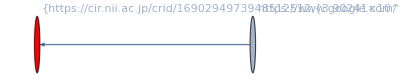
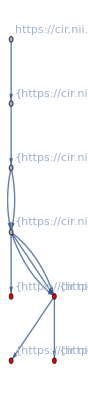
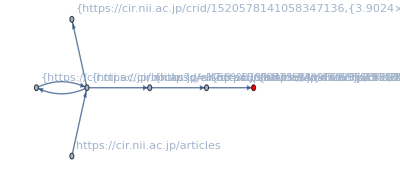
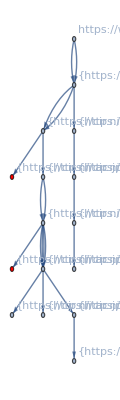
{{20230830,{101,1},-Graphics-},{20230830,{304,1},-Graphics-},{20230830,{1555,1},-Graphics-},{20230830,{5425,1},-Graphics-},{20230830,{5499,1},-Graphics-},{20230830,{6172,1},-Graphics-},{20230830,{6216,1},-Graphics-},{20230830,{8758,1},-Graphics-},{20230830,{13806,1},-Graphics-},{20230830,{14880,1},-Graphics-},{20230830,{16195,1},-Graphics-},{20230830,{16195,1},-Graphics-},{20230830,{16195,1},-Graphics-},{20230830,{16471,1},-Graphics-},{20230830,{19670,1},-Graphics-},{20230830,{20126,1},-Graphics-},{20230830,{23379,1},-Graphics-},{20230830,{25044,1},-Graphics-},{20230830,{25925,1},-Graphics-},{20230830,{26445,1},-Graphics-},{20230830,{33410,1},-Graphics-},{20230830,{33479,1},-Graphics-},{20230830,{33512,1},-Graphics-},{20230830,{33688,1},-Graphics-},{20230830,{41938,1},-Graphics-},{20230830,{42694,1},-Graphics-},{20230830,{46412,1},-Graphics-},{20230830,{46412,1},-Graphics-},{20230830,{47666,1},-Graphics-},{20230830,{48276,1},-Graphics-},{20230830,{56889,1},-Graphics-},{20230830,{60976,1},-Graphics-},{20230830,{65086,1},-Graphics-},{20230830,{65313,1},-Graphics-},{20230830,{67071,1},-Graphics-},{20230830,{67420,1},-Graphics-},{20230830,{70373,1},-Graphics-},{20230830,{70373,1},-Graphics-},{20230830,{71308,1},-Graphics-},{20230830,{72708,1},-Graphics-},{20230830,{77953,1},-Graphics-},{20230830,{80636,1},-Graphics-},{20230830,{86359,1},-Graphics-},{20230830,{86387,1},-Graphics-},{20230830,{93785,1},-Graphics-},{20230830,{93785,1},-Graphics-},{20230830,{93785,1},-Graphics-},{20230830,{97702,1},-Graphics-},{20230830,{98377,1},-Graphics-},{20230830,{101094,1},-Graphics-},{20230830,{101369,1},-Graphics-},{20230830,{102631,1},-Graphics-},{20230830,{102631,1},-Graphics-},{20230830,{102917,1},-Graphics-},{20230830,{108694,1},-Graphics-},{20230830,{111463,1},-Graphics-},{20230830,{115885,1},-Graphics-},{20230830,{116398,1},-Graphics-},{20230830,{116398,1},-Graphics-},{20230830,{116690,1},-Graphics-},{20230830,{117843,1},-Graphics-},{20230830,{121696,1},-Graphics-},{20230830,{121696,1},-Graphics-},{20230830,{125156,1},-Graphics-},{20230830,{125429,1},-Graphics-},{20230830,{125441,1},-Graphics-}}

```mathematica
ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]]
```

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

Part::partd: Part specification https://www.google.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://search.yahoo.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

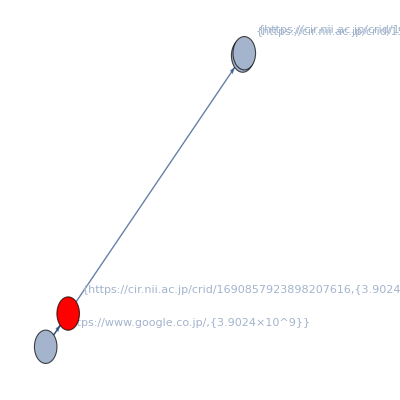
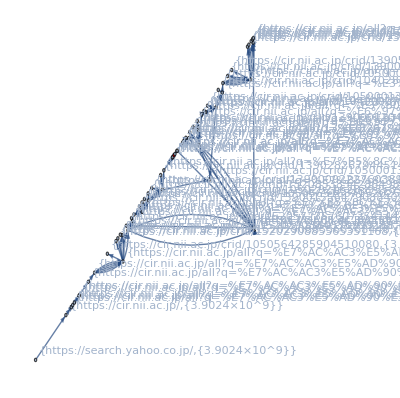
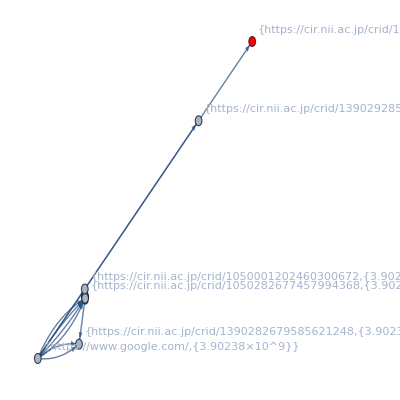
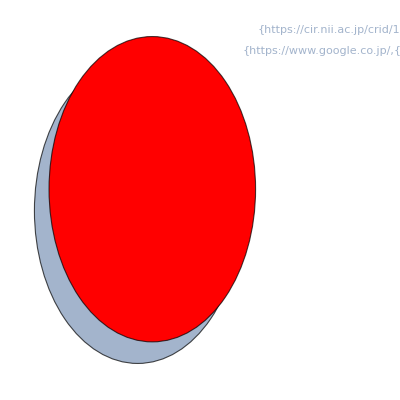
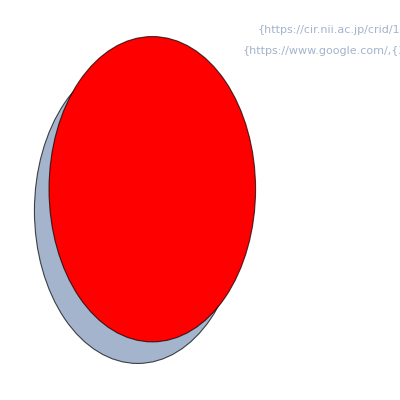
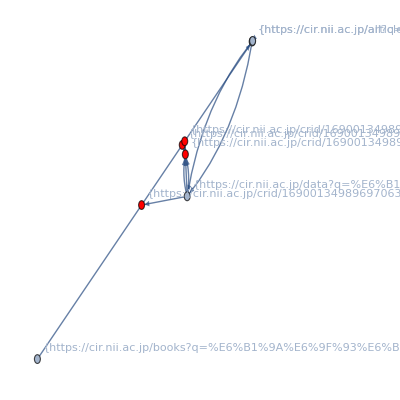
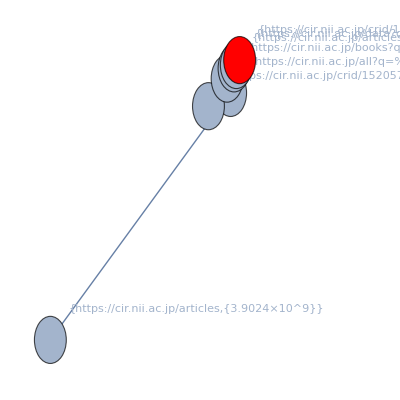
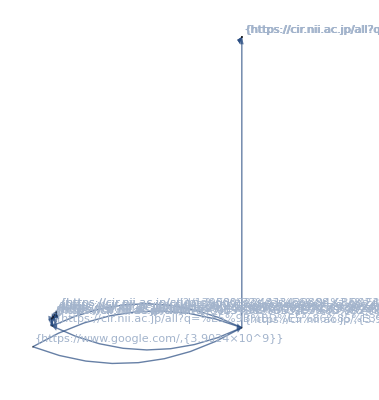
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]]
```

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 14988323
2551197

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 171
11
179 | 121
7
121

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 216734
66

```mathematica
MapApply[List,EdgeList[ckanGrPRselHLTL[4][[1]]]]
```

{{{https://cir.nii.ac.jp/crid/1570009749413847296,{3.9024×10^9}},{https://cir.nii.ac.jp/crid/1390001204709910656,{3.9024×10^9}},{3.9024×10^9,336}},{{https://www.google.co.jp/,{3.9024×10^9}},{https://cir.nii.ac.jp/crid/1570009749413847296,{3.9024×10^9}},{3.9024×10^9,335}},{{https://www.google.co.jp/,{3.9024×10^9}},{https://cir.nii.ac.jp/crid/1690857923898207616,{3.9024×10^9}},{3.9024×10^9,328}}}

```mathematica
(exp=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{66}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230830/T=4/_story

```mathematica
(*Export["ckanedgelist.json",exp]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.909048802521382×10^9

```mathematica
end-start
```

846.572713